```mathematica
Clear["Global`*"]
Needs["FEMAddOns`"]
normDt = Table[{0,0},{i,1,5}];
```

## Eval Group

Piecewise[{{(-6.75 z^6-15.75 z^4 ρ^2-11.25 z^2 ρ^4-2.25 ρ^6)/((z^2+ρ^2)^7), √(z^2+ρ^2)>1.}, {(-6.75 z^14-31.5 z^12 ρ^2-47.25 z^10 ρ^4+2.84217×10^-14 z^8 ρ^6+78.75 z^6 ρ^8+94.5 z^4 ρ^10+47.25 z^2 ρ^12+9. ρ^14)/((z^2+ρ^2)^6), True}}]

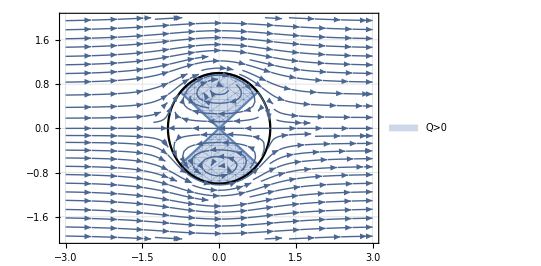

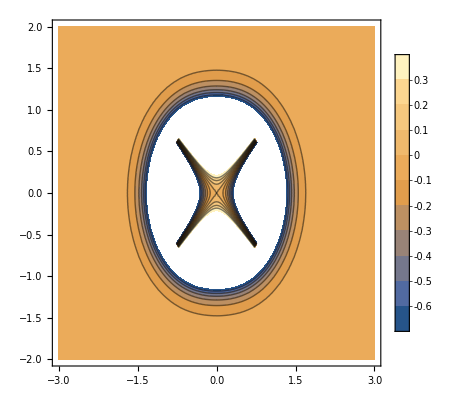

-Graphics3D-

```mathematica
uc = 1.0;
psi= uc/2 r^2(Sin[θ])^2(1-r^2);
vr= 1/(r^2(Sin[θ]))D[psi, θ];
vth= -1/(r*Sin[θ])D[psi, r];
Curl[{vr,vth,0},{r, θ, ϕ}, "Spherical"];
G =Grad[{vr,vth,0},{r, θ, ϕ}, "Spherical"];
S =Simplify[ (G + Gᵀ)/2];
Ω = Simplify[ (G - Gᵀ)/2];
Q =0.5*((Norm[Ω, "Frobenius"])^2-(Norm[S,"Frobenius"])^2);
psi2=TransformedField["Spherical"->"Cylindrical",psi,{r,θ,ϕ}->{ρ,Θ,z}];
(*Latex*)
Subscript[U, c]=1.0;a=1.0;
psi2= Subscript[U, c]/2 ρ^2(1-a^3/((ρ^2+z^2)^(3/2)));
psi2=Piecewise[{{(-3 Subscript[U, c])/4 ρ^2(1-(ρ^2+z^2)/a^2),Sqrt[ρ^2+z^2]≤ a},{Subscript[U, c]/2 ρ^2(1-a^3/((ρ^2+z^2)^(3/2))),Sqrt[ρ^2+z^2]>a}}];
psi2=Boole[Sqrt[ρ^2+z^2]≤ a]((-3 Subscript[U, c])/4 ρ^2(1-(ρ^2+z^2)/a^2))+Boole[Sqrt[ρ^2+z^2]>a](Subscript[U, c]/2 ρ^2(1-a^3/((ρ^2+z^2)^(3/2))));
vrho= -1/ρ D[psi2, z];
vz= 1/ρ D[psi2, ρ];
FullSimplify[vrho];
FullSimplify[vz];
Curl[{vrho,0,vz},{ρ, Θ, z}, "Cylindrical"];
G2 =Grad[{vrho,0,vz},{ρ, Θ, z}, "Cylindrical"];
S2 =Simplify[ (G2 + G2ᵀ)/2] ;
Ω2 = Simplify[ (G2 - G2ᵀ)/2];
Q =0.5*((Norm[Ω2, "Frobenius"])^2-(Norm[S2,"Frobenius"])^2);
FullSimplify[Q2]
Q2test=TransformedField["Spherical"->"Cylindrical",Q,{r,θ,ϕ}->{ρ,Θ,z}];
FullSimplify[Q2test];
p1 = RegionPlot[{Q>0},{z,-3,3},{ρ,-2,2},PlotTheme->"Detailed",AspectRatio->2/3];
p2 = PolarPlot[a,{t,0,2*Pi},PlotStyle->Black,AspectRatio->2/3];
p3 = StreamPlot[{vz,vrho},{z,-3,3},{ρ,-2,2},StreamPoints->Fine,AspectRatio->2/3];
Show[p1,p2,p3]
ContourPlot[Q2, {z,-3,3}, {ρ, -2,2}, Contours->10, PlotLegends->Automatic]
Plot3D[Q2, {z,-3,3}, {ρ, -3, 3}]
```

```mathematica
(*Rankine Vortex*)
uc = 1.0;
psi= uc/2 r^2(Sin[θ])^2(1-r^2);
vr= 0;
vth= Γ/(2*Pi*r);
Curl[{vr,vth,0},{r, θ, ϕ}, "Spherical"];
G =Grad[{vr,vth,0},{r, θ, ϕ}, "Spherical"]
S =Simplify[ (G + Gᵀ)/2];
Ω = Simplify[ (G - Gᵀ)/2];
Q =0.5*((Norm[Ω, "Frobenius"])^2-(Norm[S,"Frobenius"])^2)
FullSimplify[Q]
```

{{0,-Γ/(2 π r^2),0},{-Γ/(2 π r^2),0,0},{0,0,(Γ Cot[θ])/(2 π r^2)}}

0.5 (-(Abs[Γ/r^2]^2)/(2 π^2)-(Abs[(Γ Cot[θ])/r^2]^2)/(4 π^2))

(Γ (-0.0253303-0.0126651 Abs[Cot[θ]]^2) Conjugate[Γ])/Abs[r]^4

```mathematica
Clear["Global`*"]
(*Burgers Vortex*)
vrho= -α*ρ;
G=1-Exp[(-α*ρ^2)/(2*ν)];
vthh = Γ/(2*Pi*ρ)(G);
vz= 2*α*z;
Print["yo"]
Curl[{vrho,vthh,vz},{ρ, Θ, z}, "Cylindrical"] //Simplify
G2 =Grad[{vrho,vthh,vz},{ρ, Θ, z}, "Cylindrical"];
S2 =Simplify[ (G2 + G2ᵀ)/2];
Ω2 = Simplify[ (G2 - G2ᵀ)/2];
Q2 =0.5*((Norm[Ω2, "Frobenius"])^2-(Norm[S2,"Frobenius"])^2);
FullSimplify[Q2]
ContourPlot[Q, {z,-3,3}, {ρ, -1, 1}];
```

{0,0,(ⅇ^(-(α ρ^2)/(2 ν)) α Γ)/(2 π ν)}

ⅇ^(-Re[(α ρ^2)/ν]) (0.00633257 Abs[(α Γ)/ν]^2-0.00633257 Abs[(α Γ)/ν-(2 (-1+ⅇ^((α ρ^2)/(2 ν))) Γ)/ρ^2]^2)-3. α Conjugate[α]

yo

{0,0,(ⅇ^(-(α ρ^2)/(2 ν)) α Γ)/(2 π ν)}

ⅇ^(-Re[(α ρ^2)/ν]) (0.00633257 Abs[(α Γ)/ν]^2-0.00633257 Abs[(α Γ)/ν-(2 (-1+ⅇ^((α ρ^2)/(2 ν))) Γ)/ρ^2]^2)-3. α Conjugate[α]